```mathematica
ClearAll["Global`*"]
```

# Diagnostic testing

## 20-02-06

## Parameters

```mathematica
t=.1;
t1 =.05; 
k1 = 10;
k2 = 20;
δ=.1;
```

## Functions

```mathematica
ProbABC[k1_, k2_, t_, t1_]:= (1-Exp[-k1 t1])*(1-Exp[-k2 (t-t1)])
```

```mathematica
ProbDerivABC[k1_, k2_, t_, t1_] := k1*(Exp[k2(t-t1)]-1)-k2*(Exp[k1*t1]-1)
```

```mathematica
Tmax[k1_, k2_, t_]:= Solve[ProbDerivABC[k1, k2, t, tmax]==0,tmax,Reals]
```

```mathematica
Manipulate[Plot[Tmax[k1,k2,t],{k1,0,1}],{k1,0,100}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of tmax→0.0549177.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Manipulate[Plot[Tmax[k1,k2,t],{t,0,1}],{k1,0,100}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of tmax→0.0549177.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{10,0.0549177},{15,0.05238},{20,0.05},{25,0.0477814},{30,0.0457208},{35,0.0438109},{40,0.0420418},{45,0.0404028},{50,0.0388832},{55,0.0374725},{60,0.0361609},{65,0.0349394},{70,0.0337998},{75,0.0327347},{80,0.0317374},{85,0.0308018},{90,0.0299227},{95,0.0290952},{100,0.028315}}

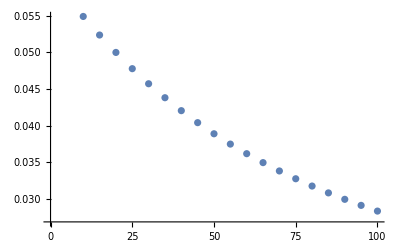

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

```mathematica
xt=Table[{k1,Tmax[k1,k2,t]}, {k1, 10, 100, 5}];
maxtimes = xt/.{{Rule[a_,b_]}}:> b
ListPlot[maxtimes]
```

## Probability tests

## T_max tests

```mathematica
tmax = Tmax[k1,k2,t][[1]]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of tmax→0.0549177.

Hold[tmax=Tmax[k1,k2,t]⟦1⟧]

## KMC diagnostic tests

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of tmax→0.0549177.